```mathematica
SetDirectory[NotebookDirectory[]];
dataCu2p=Import["D:\\Experiments\\LEED_ARPES_Analysis\\Cu2p_1200eV.txt","Data"];
data1200eV=Import["D:\\Experiments\\LEED_ARPES_Analysis\\overview1200eV.txt","Data"];
data1300eV=Import["D:\\Experiments\\LEED_ARPES_Analysis\\Overview1300eV.txt","Data"];
```

```mathematica
dataCu2p[[1]]
```

{230,49.3434}

```mathematica
data1200eV[[1]]
```

{200,102.694}

```mathematica
FindPeaks[data1200eV[[60;;200]][[All,2]],4]
```

{{12,100.117},{37,169.657},{77,223.547}}

```mathematica
data1200eV[[60;;200]][[All,1]][[37]]
data1200eV[[60;;200]][[All,1]][[77]]
```

247.524

267.533

```mathematica
1200-267.533432392273-4.94
```

927.527

```mathematica
FindPeaks[data1300eV[[30;;200]][[All,2]],8]
```

{{4,20.0658},{69,42.5157},{108,63.4812}}

```mathematica
data1300eV[[30;;200]][[All,1]][[69]]
data1300eV[[30;;200]][[All,1]][[108]]
```

348.524

368.034

```mathematica
Show[ListLinePlot[{data1200eV,data1300eV},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"1200 eV", "1300 eV"}],FrameLabel->{"E_k (eV)", "Intensity"}]
```

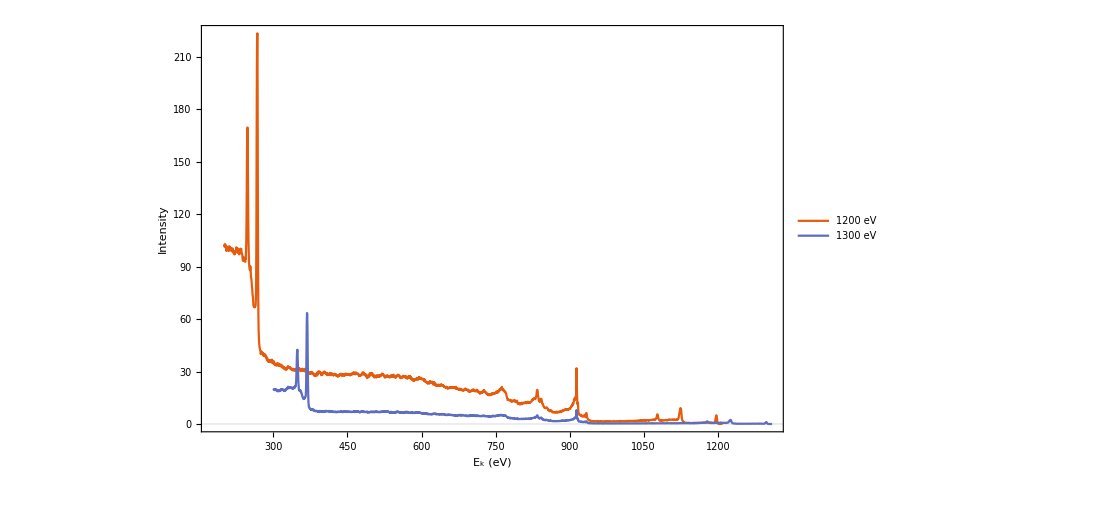

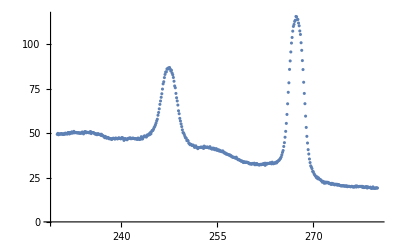

```mathematica
ListPlot[dataCu2p]
Show[ListLinePlot[{data1200eV[[60;;200]],data1300eV[[30;;200]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"1200 eV", "1300 eV"}],FrameLabel->{"E_k (eV)", "Intensity"}]
```

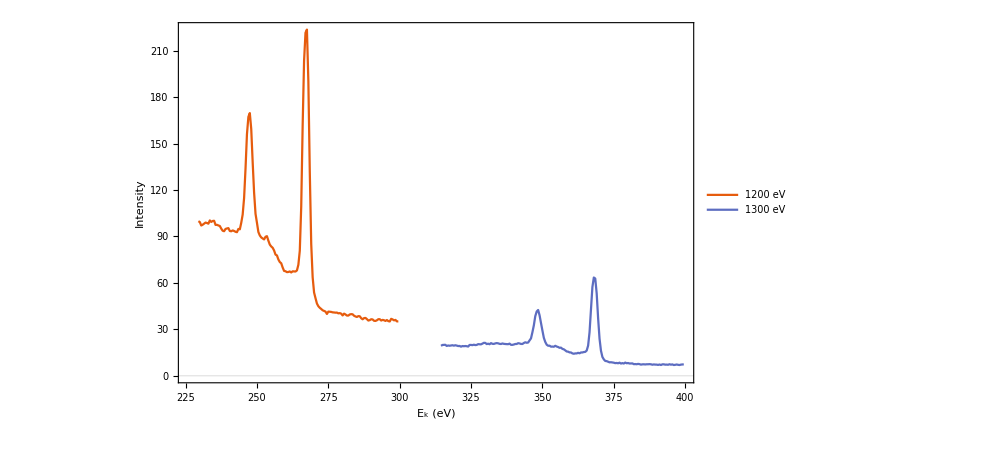

```mathematica
SurfaceState=Import["D:\\Experiments\\LEED_ARPES_Analysis\\surface_state.txt","Data"][[2;;-1,All]];
```

```mathematica
yscale=Table[54+(55.5-54)(i-1)/301,{i,1,301}];
xscale=Table[-10+20 (i-1)/507,{i,1,507}];
```

```mathematica
surfaceData =Flatten[Table[Table[{xscale[[i]],yscale[[j]],SurfaceState[[i,j]]},{j,1,301}],{i,1,507}],1];
```

```mathematica
surfaceData//Length
```

152607

```mathematica
ListDensityPlot[surfaceData]
```

-Graphics-

```mathematica
Show[%31,FrameLabel->{{HoldForm["\!\(\*SubscriptBox[\(E\), \(k\)]\) (eV)"],None},{HoldForm[Angle °],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
band4s={};
For[i=1,i<=Length[surfaceData],i++,
If[surfaceData[[i]][[1]]>=-3.3&&surfaceData[[i]][[1]]<=3.2&&surfaceData[[i]][[2]]>=54.55&&surfaceData[[i]][[2]]<=55.05,
AppendTo[band4s,surfaceData[[i]]];
];
]
Show[ListDensityPlot[band4s,PlotLegends->Automatic],FrameLabel->{"Angle (degree)", "E_k (eV)"}]
```

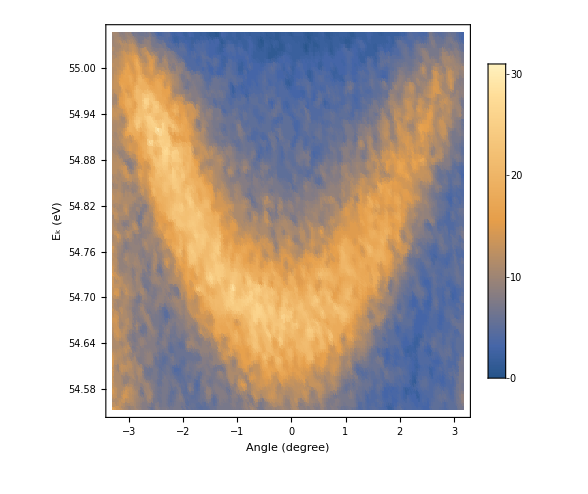

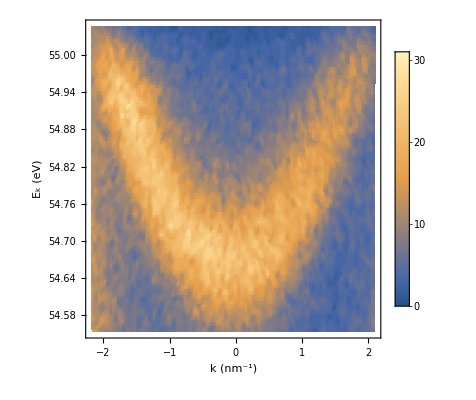

```mathematica
rescaledBand4s={};
hb=6.626*10^(-34)/(2Pi);
me=9.1093837*10^(-31);
ee=1.6*10^(-19);

For[i=1,i<=Length[band4s],i++,
AppendTo[rescaledBand4s,{Sqrt[2 me band4s[[i]][[2]] ee]Sin[band4s[[i]][[1]] Pi/180]*10^(-9)/hb,band4s[[i]][[2]],band4s[[i]][[3]]}]
]
Show[ListDensityPlot[rescaledBand4s,PlotLegends->Automatic],FrameLabel->{"k (nm^-1)", "E_k (eV)"}]
```

```mathematica
filteredBand={};
thr=18;
For[i=1,i<=Length[rescaledBand4s],i++,
AppendTo[filteredBand,{rescaledBand4s[[i]][[1]],rescaledBand4s[[i]][[2]],
If[rescaledBand4s[[i]][[3]]>=thr,
rescaledBand4s[[i]][[3]],
0
]
}]
]

Show[ListDensityPlot[filteredBand,PlotLegends->Automatic],FrameLabel->{"k (nm^-1)", "E_k (eV)"}]
```

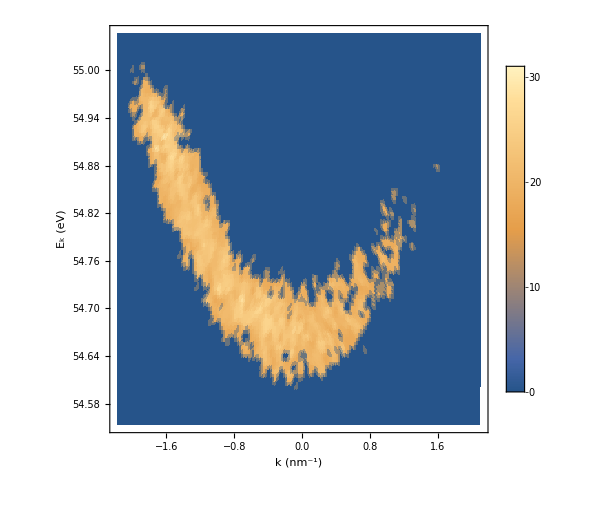

```mathematica
bandSorted=SortBy[filteredBand,First];
```

```mathematica
filteredBand[[All,1]]//Sort//Union
```

```mathematica
steps=Table[-2.18253+(2.10419+2.18253)i/400,{i,0,400}];
d=(2.10419+2.18253)/400
```

0.0107168

```mathematica
vals={};
data={};
For[i=1,i<=401,i++,
t=steps[[i]];
temp={};
For[j=1,j<=Length[filteredBand],j++,
If[filteredBand[[j]][[1]]<=t+0.5d&&filteredBand[[j]][[1]]>=t-0.5d,
AppendTo[temp,filteredBand[[j]]];
];
];

y=0;
sum=0;
For[j=1,j<=Length[temp],j++,
y=y+temp[[j]][[2]]*temp[[j]][[3]];
sum=sum+temp[[j]][[3]];
];

If[y!=0,
AppendTo[data,{t,y/sum}];
]
]
```

```mathematica
Show[ListPlot[data,PlotTheme->"Scientific"],Plot[54.673762056786295+0.0009741172945034742 x+0.08132004658941298 x^2,{x,-2.18253,2.10419},PlotLegends->{54.6738+0.001 k+0.0813 k^2}],FrameLabel->{"k (nm^-1)", "E_k (eV)"}]
```

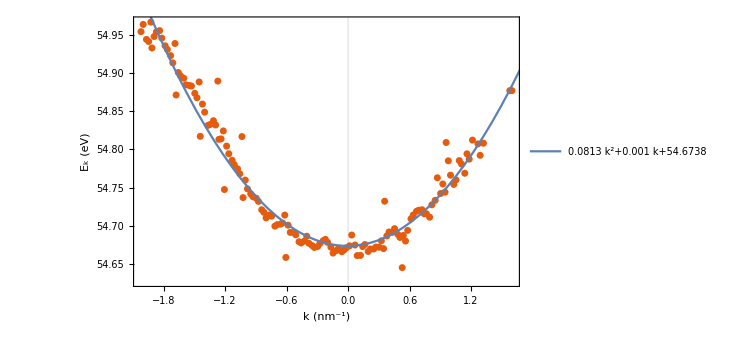

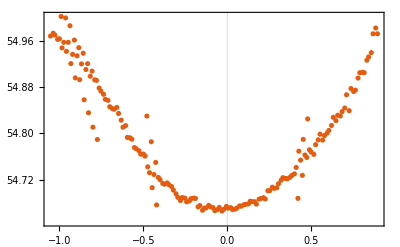

```mathematica
ListPlot[data,PlotTheme->"Scientific"]
```

```mathematica
Fit[data,{1,x,x^2},x]
```

54.6738+0.000974117 x+0.08132 x^2

```mathematica
(hb^2/(2 0.08132004658941298*ee*10^(-18)))/me
```

0.469144

```mathematica
me=9.1093837*10^(-31);
```